```mathematica
data0=ResourceData["Epidemic Data for Novel Coronavirus COVID-19"]
```

Dataset[<>]

```mathematica
DeleteObject[ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"]]
```

```mathematica
datacn=ResourceData["Epidemic Data for Novel Coronavirus COVID-19","ChinaProvinces"]
```

Dataset[<>]

```mathematica
{infected,recovered,deceased}=
Normal@datacn[SelectFirst[#AdministrativeDivision==LinguisticAssistant&],
{#ConfirmedCases-(#RecoveredCases+#Deaths),#RecoveredCases,#Deaths}&]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
{infected,recovered,deceased}=TimeSeriesWindow[#,{{2020,1,1},{2020,6,30}}]&/@%181
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…]}

重现湖北省确诊病例的变化

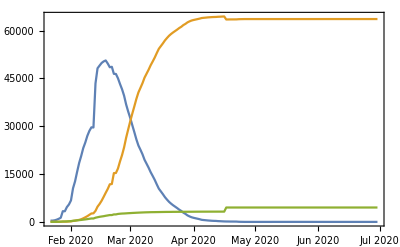

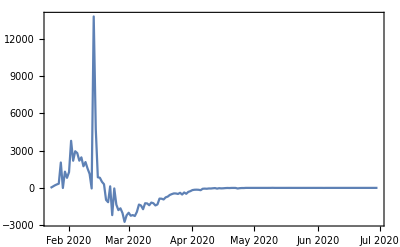

```mathematica
DateListPlot[Differences[infected],PlotRange->Full]
```